```mathematica
Clear[R, V, S, ϵ,p];
```

```mathematica
Eigenvalues[{{-R1*V-ϵ,-R1*S,-R0*S},{R1*V,R1*S-γ,0},{0,0,R0*S-1}}]
```

{-1+R0 S,1/2 (R1 S-R1 V-γ-ϵ-√((-R1 S+R1 V+γ+ϵ)^2-4 (R1 V γ-R1 S ϵ+γ ϵ))),1/2 (R1 S-R1 V-γ-ϵ+√((-R1 S+R1 V+γ+ϵ)^2-4 (R1 V γ-R1 S ϵ+γ ϵ)))}

```mathematica
Simplify[1/2 (-1-epsilon-ⅈ R+R S-R V+√((-1-epsilon-ⅈ R+R S-R V)^2+4 (-epsilon-ⅈ R+epsilon R S-R V)))]
```

1/2 (-1-epsilon-ⅈ R+R S-R V+√(4 epsilon (-1+R S)-4 R (ⅈ+V)+(1+epsilon+R (ⅈ-S+V))^2))

```mathematica
S=((R0+γ-√(R0^2-2*R0*γ+γ^2+4*p*R0*γ))/(2R0))
```

0.423695

```mathematica
-1+R1 S
```

0.906625

```mathematica
p=0.5
```

0.5

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
R0=4.5
```

4.5

```mathematica
R1=2.5
```

2.5

```mathematica
γ=1
```

1

```mathematica
Clear[p,γ,R1,R0,S,ϵ]
```

```mathematica
f[p_]:=35./(63.-81. p)
```

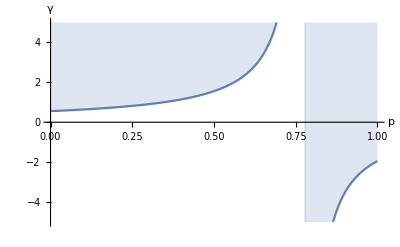

```mathematica
Plot[f[p],{p,0,1},PlotRange->{{0,1},{-5,5}},AxesLabel->{p,γ},Filling->Top]
```

```mathematica
Solve[-1+0.9 (2.5+γ-√(6.25-5. γ+10. p γ+γ^2))==0,γ]
```

{{γ→35./(63.-81. p)}}

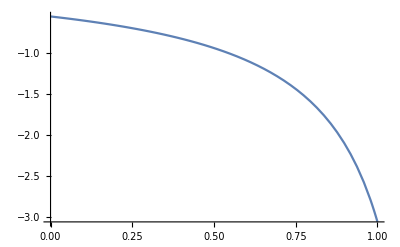

```mathematica
Plot[f[p],{p,0,1}]
```

```mathematica
Solve[{ϵ*(1-p)-R1*S*V-R0*S*Ihat-ϵ*S==0,R1*S*V+ϵ*p-γ*V==0,R0*S*Ihat-Ihat==0},{S,V,Ihat}]
```

{{S→1/R0,V→(p R0 ϵ)/(-R1+R0 γ),Ihat→(R1 ϵ-R0 R1 ϵ-R0 γ ϵ+R0^2 γ ϵ-p R0^2 γ ϵ)/(R0 (-R1+R0 γ))},{S→(R1+γ-√(R1^2-2 R1 γ+4 p R1 γ+γ^2))/(2 R1),V→(ϵ-(γ ϵ)/R1+(√(R1^2-2 R1 γ+4 p R1 γ+γ^2) ϵ)/R1)/(2 γ),Ihat→0},{S→(R1+γ+√(R1^2-2 R1 γ+4 p R1 γ+γ^2))/(2 R1),V→(ϵ-(γ ϵ)/R1-(√(R1^2-2 R1 γ+4 p R1 γ+γ^2) ϵ)/R1)/(2 γ),Ihat→0}}

```mathematica
(p R0 ϵ)/(-R1+R0 γ)
```

0.00135453

```mathematica
(R1 ϵ-R0 R1 ϵ-R0 γ ϵ+R0^2 γ ϵ-p R0^2 γ ϵ)/(R0 (-R1+R0 γ))
```

0.111111 (0.0084282-0.0243816 p)

```mathematica
(R1+γ-√(R1^2-2 R1 γ+4 p R1 γ+γ^2))/(2 R1)
```

0.0291796

```mathematica
p=0.1
```

0.1

```mathematica
(R1+γ+√(R1^2-2 R1 γ+4 p R1 γ+γ^2))/(2 R1)
```

1.37082

```mathematica
(ϵ-(γ ϵ)/R1+(√(R1^2-2 R1 γ+4 p R1 γ+γ^2) ϵ)/R1)/(2 γ)
```

0.000795327

```mathematica
0.00842819614711033/0.024381567425569177
```

0.345679

```mathematica
f[0.3456790123456789]
```

1.

```mathematica
(R1+γ-√(R1^2-2 R1 γ+4 p R1 γ+γ^2))/(2 R1)
```

0.339445

```mathematica
(ϵ-(γ ϵ)/R1+(√(R1^2-2 R1 γ+4 p R1 γ+γ^2) ϵ)/R1)/(2 γ)
```

0.000795327

```mathematica
Eigenvalues[{{-R1*V-ϵ,-R1*S,-R0*S},{R1*V,0,0},{R0*Ihat,0,0}}]
```

{0,0.5 (-0.00120403-0.00677266 p-√(-0.0168549+0.0337291 p+0.0000458689 p^2)),0.5 (-0.00120403-0.00677266 p+√(-0.0168549+0.0337291 p+0.0000458689 p^2))}